```mathematica
confirmed = 
  Import["https://raw.githubusercontent.com/CSSEGISandData/COVID-19/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"
];
confirmed[[1]][[-1]]
```

4/9/20

```mathematica
deaths = Import[
   "https://raw.githubusercontent.com/CSSEGISandData/COVID-19/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_deaths_global.csv"
];
deaths[[1]][[-1]]
```

4/9/20

```mathematica
confirmedData = 
 AssociationThread[First@confirmed, #] & /@ Rest[confirmed] // Dataset
```

Dataset[<>]

```mathematica
deathData = 
 AssociationThread[First@deaths, #] & /@ Rest[deaths] // Dataset
```

Dataset[<>]

```mathematica
keys = Keys[First@Normal@confirmedData];
Keys[First@Normal@deathData];
% == keys
```

True

```mathematica
logistic = L/(1 + Exp[-k (t - t0)])  (*for NonlinearModelFit*)
```

L/(1+ⅇ^(-k (t-t0)))

```mathematica
(*Germany / Deutschland*)
```

```mathematica
DECaseData = 
confirmedData@Select[#"Country/Region" == "Germany" &];
DEDeathData = 
 deathData@Select[#"Country/Region" == "Germany" &];
```

```mathematica
deathCases = 
Transpose[{Range[Length@keys - 4], 
Values@Normal[DEDeathData[Total, Drop[keys, 4]]]}];
```

```mathematica
confirmedCases = 
Transpose[{Range[Length@keys - 4], 
Values@Normal[DECaseData[Total, Drop[keys, 4]]]}];
```

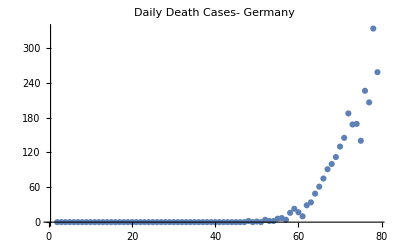

```mathematica
ListPlot[Transpose[{Rest[deathCases[[All, 1]]], 
 Differences[deathCases[[All, 2]]]}], PlotRange -> All, PlotLabel->"Daily Death Cases- Germany"]
```

```mathematica
deathCasesNLM = 
NonlinearModelFit[deathCases, 
logistic, {{k, 0.3}, {L, 3000}, {t0, 17}}, t];
deathCasesNLM@"BestFitParameters"
```

{k→0.217671,L→4220.39,t0→77.0636}

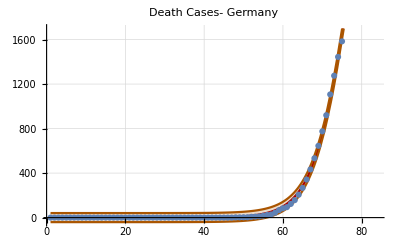

```mathematica
deathBands[t_] = 
  deathCasesNLM["SinglePredictionBands", ConfidenceLevel -> 0.95];
dth0 = Plot[{deathCasesNLM[t], deathBands[t]}, {t, 1, 
    deathCases[[-1]][[1]] + 5}, Filling -> {2 -> {1}}, 
   PlotStyle -> {Darker@Red, Darker@Orange, Darker@Orange}, 
   GridLines -> Automatic, PlotLabel -> "Death Cases- Germany"];
dth1 = ListPlot[deathCases, PlotRange -> All];
Show[dth0, dth1]
```

```mathematica
deathCasesNLM@"ParameterConfidenceIntervalTable"
```

| Estimate | Standard Error | Confidence Interval
k | 0.217671 | 0.00446128 | {0.208786,0.226557}
L | 4220.39 | 158.335 | {3905.04,4535.75}
t0 | 77.0636 | 0.347956 | {76.3706,77.7566}

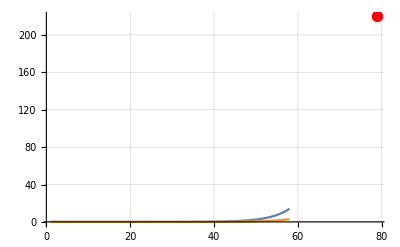

```mathematica
daynum = deathCases[[-1]][[1]];
Show[Plot[{deathCasesNLM'[t], deathCasesNLM''[t]}, {t, 1, 58}, 
GridLines -> Automatic, PlotRange -> All], 
 ListPlot[Tooltip@{{daynum, deathCasesNLM'[daynum]}}, 
 PlotStyle -> {Red, PointSize[0.02]}]]
```

```mathematica
confirmedNLM = 
NonlinearModelFit[confirmedCases, 
logistic, {{k, 0.3}, {L, 80000}, {t0, 17}}, t];
confirmedNLM["BestFitParameters"]
```

{k→0.192083,L→130854.,t0→68.6743}

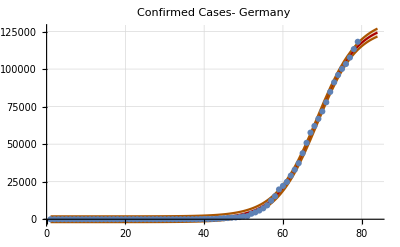

Show::gtype: Out is not a type of graphics.

```mathematica
confirmedBands[t_] = 
 confirmedNLM["SinglePredictionBands", 
  ConfidenceLevel -> 0.95]; cnf0 = 
 Plot[{confirmedNLM[t], confirmedBands[t]}, {t, 1, 
   confirmedCases[[-1]][[1]] + 5}, Filling -> {2 -> {1}}, 
  PlotStyle -> {Darker@Red, Darker@Orange, Darker@Orange}, 
  GridLines -> Automatic, PlotLabel -> "Confirmed Cases- Germany"];
cnf1 = ListPlot[confirmedCases, PlotRange -> All];
Show[cnf0, cnf1]
```

```mathematica
(*Show[%271,ImageSize->Large]*)
```

Show::gtype: Out is not a type of graphics.

Show[%271,ImageSize→Large]

```mathematica
confirmedNLM@"ParameterConfidenceIntervalTable"
```

| Estimate | Standard Error | Confidence Interval
k | 0.192083 | 0.00281551 | {0.186476,0.197691}
L | 130854. | 1369.38 | {128126.,133581.}
t0 | 68.6743 | 0.146005 | {68.3835,68.9651}

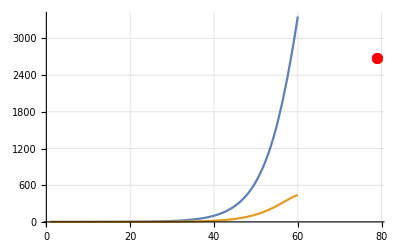

```mathematica
daynum = confirmedCases[[-1]][[1]];
Show[Plot[{confirmedNLM'[t], confirmedNLM''[t]}, {t, 1,60}, 
  GridLines -> Automatic, PlotRange -> All], 
 ListPlot[Tooltip@{{daynum, confirmedNLM'[daynum]}}, 
  PlotStyle -> {Red, PointSize[0.02]}]]
```

```mathematica
(*Bangladesh*)
BDCaseData = 
confirmedData@Select[#"Country/Region" == "Bangladesh" &];
BDDeathData = 
 deathData@Select[#"Country/Region" == "Bangladesh" &];
```

```mathematica
BDdeathCases = 
Transpose[{Range[Length@keys - 4], 
Values@Normal[BDDeathData[Total, Drop[keys, 4]]]}];
```

```mathematica
BDconfirmedCases = 
Transpose[{Range[Length@keys - 4], 
Values@Normal[BDCaseData[Total, Drop[keys, 4]]]}];
```

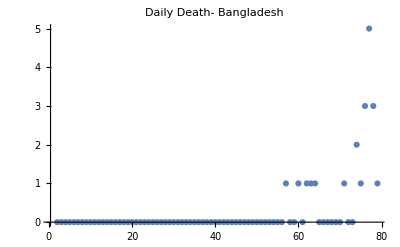

```mathematica
ListPlot[Transpose[{Rest[BDdeathCases[[All, 1]]], 
 Differences[BDdeathCases[[All, 2]]]}], PlotRange -> All, PlotLabel->"Daily Death- Bangladesh"]
```

```mathematica
BDdeathCasesNLM = 
NonlinearModelFit[BDdeathCases, 
logistic, {{k, 0.3}, {L, 3000}, {t0, 17}}, t];
BDdeathCasesNLM@"BestFitParameters"
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{k→0.0576191,L→3.88189,t0→26.4794}

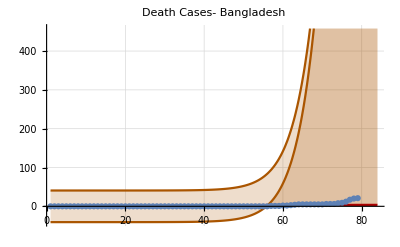

```mathematica
BDdeathBands[t_] = 
  deathCasesNLM["SinglePredictionBands", ConfidenceLevel -> 0.95];
dth0 = Plot[{BDdeathCasesNLM[t], BDdeathBands[t]}, {t, 1, 
    BDdeathCases[[-1]][[1]] + 5}, Filling -> {2 -> {1}}, 
   PlotStyle -> {Darker@Red, Darker@Orange, Darker@Orange}, 
   GridLines -> Automatic, PlotLabel -> "Death Cases- Bangladesh"];
dth1 = ListPlot[BDdeathCases, PlotRange -> All];
Show[dth0, dth1]
```

```mathematica
BDdeathCasesNLM@"ParameterConfidenceIntervalTable"
```

| Estimate | Standard Error | Confidence Interval
k | 0.0576191 | 0.0711777 | {-0.0841436,0.199382}
L | 3.88189 | 1.86415 | {0.169111,7.59467}
t0 | 26.4794 | 23.7655 | {-20.8536,73.8124}

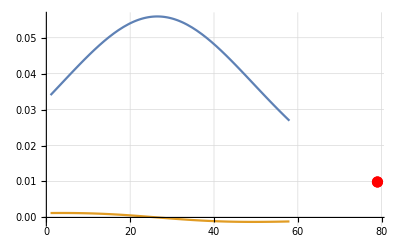

```mathematica
BDdaynum = BDdeathCases[[-1]][[1]];
Show[Plot[{BDdeathCasesNLM'[t], BDdeathCasesNLM''[t]}, {t, 1, 58}, 
GridLines -> Automatic, PlotRange -> All], 
 ListPlot[Tooltip@{{BDdaynum, BDdeathCasesNLM'[BDdaynum]}}, 
 PlotStyle -> {Red, PointSize[0.02]}]]
```

```mathematica
(*end = x /. FindRoot[BDdeathCasesNLM'[x] == 1, {x, 30}][[1]]
DatePlus[{2020, 1, 21}, Ceiling@end]*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

31.9546

{2020,2,22}

```mathematica
BDconfirmedNLM = 
NonlinearModelFit[BDconfirmedCases, 
logistic, {{k, 0.3}, {L, 80000}, {t0, 17}}, t];
BDconfirmedNLM["BestFitParameters"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{k→0.0712203,L→38.9653,t0→24.9952}

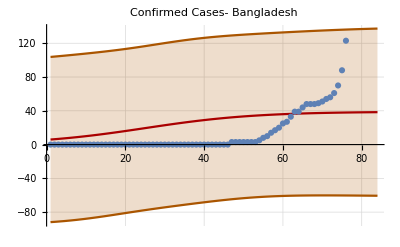

```mathematica
BDconfirmedBands[t_] = 
 BDconfirmedNLM["SinglePredictionBands", 
  ConfidenceLevel -> 0.95]; 
cnf0 = Plot[{BDconfirmedNLM[t], BDconfirmedBands[t]}, {t, 1, 
   BDconfirmedCases[[-1]][[1]] + 5}, Filling -> {2 -> {1}}, 
  PlotStyle -> {Darker@Red, Darker@Orange, Darker@Orange}, 
  GridLines -> Automatic, PlotLabel -> "Confirmed Cases- Bangladesh"];
cnf1 = ListPlot[BDconfirmedCases, PlotRange -> All];
Show[cnf0, cnf1]
```

```mathematica
BDconfirmedNLM@"ParameterConfidenceIntervalTable"
```

| Estimate | Standard Error | Confidence Interval
k | 0.0712203 | 0.0920348 | {-0.112083,0.254523}
L | 38.9653 | 15.963 | {7.17211,70.7584}
t0 | 24.9952 | 19.3028 | {-13.4497,63.4401}

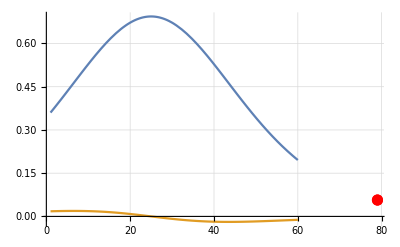

```mathematica
BDdaynum = BDconfirmedCases[[-1]][[1]];
Show[Plot[{BDconfirmedNLM'[t], BDconfirmedNLM''[t]}, {t, 1,60}, 
  GridLines -> Automatic, PlotRange -> All], 
 ListPlot[Tooltip@{{BDdaynum, BDconfirmedNLM'[BDdaynum]}}, 
  PlotStyle -> {Red, PointSize[0.02]}]]
```

```mathematica
(* End of epidemic calculation on the assumption that the last integer case per day signals the end of the epidemic.The red dot on the graph above shows the current point on the first derivative curve. The second derivative curve is also shown.*)
```

```mathematica
end = x /. FindRoot[BDconfirmedNLM'[x] == 1, {x, 30}][[1]]
DatePlus[{2020, 1, 21}, Ceiling@end]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

24.9952

{2020,2,15}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[t]→(ⅇ^(k t) L)/(ⅇ^(k t)+ⅇ^(k t0))}}

True

True

{{t→t0}}

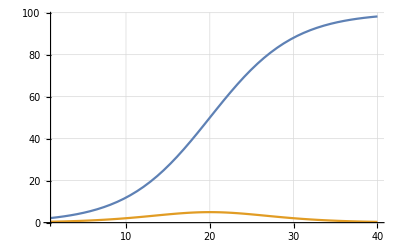

1/(1+ⅇ^(-(x-μ)/σ))

1/(1+ⅇ^(-(x-μ)/σ))

```mathematica
(*Logistic Equation*)
DSolve[{f'[t]==k f[t] (1-f[t]/L),f[t0]==L/2},f[t],t]//FullSimplify
FullSimplify[(ⅇ^(k t) L)/(ⅇ^(k t)+ⅇ^(k t0))==L/(1+E^(-k (t-t0)))]
logisticGrowth[t_,{t0_,k_,L_}]:=L/(1+E^(-k (t-t0)));
D[logisticGrowth[t,{t0,k,L}],t]==k logisticGrowth[t,{t0,k,L}] (1-logisticGrowth[t,{t0,k,L}]/L)//FullSimplify
Solve[D[logisticGrowth[t,{t0,k,L}],{t,2}]==0,t,Reals]
Plot[{logisticGrowth[t,{20,0.2,100}],Evaluate@D[logisticGrowth[t,{20,0.2,100}],t]},{t,1,40},GridLines->Automatic,PlotRange->All]
logisticGrowth[x,{μ,1/σ,1}]
CDF[LogisticDistribution[μ,σ],x]
```